### Constants

```mathematica
e = 1.6*10^-19;
R = 8.315;
T = 273 + 25;
ϵ = 8.8542*10^-12 * 80.4;
F = 96485.3;
```

### Code

```mathematica
canv = Region@ImplicitRegion[{0≤ x ≤ 50, 0≤ y ≤ 50}, {x, y}];
elect1 = Region@ImplicitRegion[{(x -25)^2 + (y - 10)^2 <= 1^2}, {x, y}];
elect2 = Region@ImplicitRegion[{(x - 25)^2 + (y - 40)^2 <= 1^2}, {x, y}];
```

```mathematica
region = RegionDifference[canv, RegionUnion[elect1, elect2]];
RegionPlot@region
```

-Graphics-

```mathematica
sol = NDSolveValue[{
Laplacian[ϕ[x, y], {x, y}] == 0, DirichletCondition[ϕ[x, y] == 1.0, (x -25)^2 + (y - 10)^2 == 1^2], DirichletCondition[ϕ[x, y] == -1.0, (x -25)^2 + (y - 40)^2 == 1^2]
}, ϕ, {x, y} ∈ region]
```

InterpolatingFunction[…]

-Graphics3D-

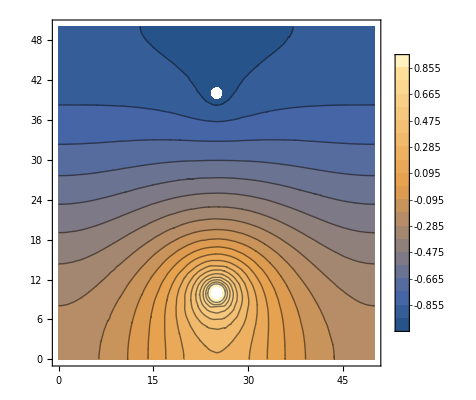

```mathematica
Plot3D[sol[x, y], {x, y} ∈ region, ColorFunction->"Rainbow", PlotLegends->Automatic]
ContourPlot[sol[x, y], {x, y} ∈ region, Contours->20, PlotLegends->Automatic]
```